```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<PlotOption`
```

## Exercise

```mathematica
OscillationData=Import["oscillation.dat"];
```

```mathematica
xList=Map[{#[[1]],#[[2]]}&,OscillationData];
```

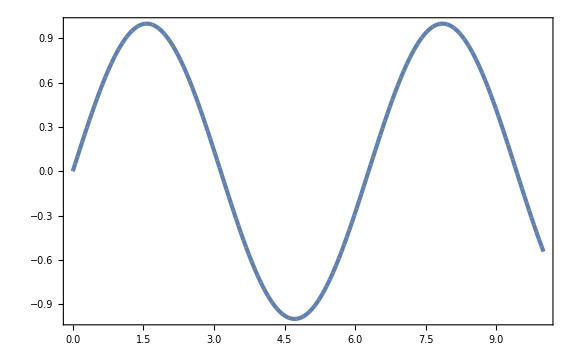

```mathematica
Show[ListPlot[xList],Plot[Sin[x],{x,0,10},PlotStyle->{Color[2],Dotted}]]
```

## NoiseMap

```mathematica
NoiseMapData=Import["NoiseMap.dat"];
```

```mathematica
num=Length[NoiseMapData]^(1/3);
```

```mathematica
deltaN=Table[Table[Table[NoiseMapData[[num^2 (nz-1)+num(ny-1)+nx,1]],{nx,num}],{ny,num}],{nz,num}];
```

```mathematica
ListDensityPlot3D[deltaN,BoxRatios->{1, 1, 1},ColorFunction->"TemperatureMap",PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
(** Fourier transformation 1<kx<num **)
```

```mathematica
ζk[kx_,ky_,kz_]=1/num^(3/2)Sum[deltaN[[xz,xy,xx]] ⅇ^(-(2π ⅈ)/num((xx-1)(kx-1)+(xy-1)(ky-1)+(xz-1)(kz-1))),{xx,num},{xy,num},{xz,num}];
```

```mathematica
(** Count Subscript[N, k] **)
```

```mathematica
norm3[x_,y_,z_]=√((x-1)^2+(y-1)^2+(z-1)^2);
```

```mathematica
normdat=Table[Table[Table[norm3[nx,ny,nz],{nx,num}],{ny,num}],{nz,num}]//Simplify;
```

```mathematica
ck=0.01;
```

```mathematica
lnk[ll_]=(1+ck)^(ll-1)-1;
```

```mathematica
klist={};lk=0;
```

```mathematica
Do[If[lnk[ii]<√3(num-1),klist=Join[klist,{lnk[ii]}];lk++;,Break;],{ii,1,1000}]
klist=Join[klist,{lnk[lk+1]}];
ksize=klist//Length;
```

```mathematica
Nklist=Table[Length[Select[Select[Flatten[Flatten[normdat]],#≥lnk[nk]&],#<lnk[nk+1]&]],{nk,ksize}];
```

```mathematica
Nk=0;ζtemp=0;
```

```mathematica
(*ζt=0 klist;ζe=Table[{0},{ksize}];
Do[Do[If[norm3[nx,ny,nz]≥klist[[ii]],If[norm3[nx,ny,nz]<klist[[ii+1]],{ζtemp=Abs[ζk[nx,ny,nz]]^2;ζt[[ii]]+=ζtemp;ζe[[ii]]=Join[ζe[[ii]],{ζtemp}];}]],{nz,num},{ny,num},{nx,num}],{ii,ksize}]//AbsoluteTiming*)
```

```mathematica
ζeList[ii_]:=Select[Flatten[Table[If[klist[[ii]]<=norm3[nx,ny,nz]<klist[[ii+1]],Abs[ζk[nx,ny,nz]]^2,None],{nz,num},{ny,num},{nx,num}],2],Positive]
```

```mathematica
ζe=ParallelTable[ζeList[ii],{ii,ksize-1}];//AbsoluteTiming
ζt=Table[Total[ζe[[ii]]],{ii,Length[ζe]}];
```

{23.357,Null}

```mathematica
tab=Table[Around[Sum[ζe[[jj,ll]],{ll,Length[ζe[[jj]]]}],If[Length[ζe[[jj]]]>1,Sqrt[Nklist[[jj]]]StandardDeviation[ζe[[jj]]],0]],{jj,Length[ζe]}];
```

```mathematica
taberr=Table[{klist[[ii]],tab[[ii]]/(num^3 ck)},{ii,Length[tab]}];
```

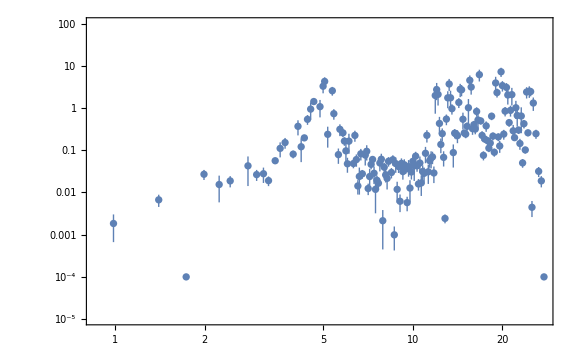

```mathematica
ListLogLogPlot[taberr,PlotRange->(*All*){10^-5,10^2},Frame->True,Joined->False]
```

```mathematica
(** Check the variance **)
```

```mathematica
flatdN=deltaN//Flatten;
```

```mathematica
(*num^-3(flatdN.flatdN)*)
Variance[flatdN]
```

1.05293

```mathematica
ck Total[ζt]/(num^3 ck)
```

1.05275

## Lattice (chaotic)

### Annimation

```mathematica
LatticeMapData=Import["Lattice.dat"];
```

```mathematica
num=Length[First[LatticeMapData]]^(1/3)
```

17

```mathematica
zetaList=Table[LatticeMapData[[efoldN,num^2 (nz-1)+num(ny-1)+nx]],{efoldN,Length[LatticeMapData]},{nx,num},{ny,num},{nz,num}];
```

```mathematica
Dzeta=3Sqrt[Variance[Last[zetaList]//Flatten]]
```

0.000451971

```mathematica
zetaPlotList=Table[ListDensityPlot3D[zetaList[[i]],BoxRatios->{1, 1, 1},Ticks->None,ColorFunction->(ColorData["TemperatureMap"][(#1/Dzeta+1)/2]&),ColorFunctionScaling->False,PlotLegends->BarLegend[{Automatic,{-Dzeta,Dzeta}},LegendLabel->OverTilde[ζ]==-H δρ/ρ̇,LabelStyle->Directive[Large,Black,FontFamily->"Palatino"]],PlotLabel->Style[N==0.1(i-1),Large,Black,FontFamily->"Palatino"],ImageSize->Large],{i,2,Length[zetaList]}];
```

```mathematica
Export["zetamap.gif",zetaPlotList];//AbsoluteTiming
```

{40.2222,Null}

```mathematica
Last[zetaPlotList]
```

-Graphics3D-

### Power Spectrum

```mathematica
NclMap=Map[#[[2]]&,Sort[Import["LatticeNcl.dat"]]];
```

```mathematica
num=Length[NclMap]^(1/3)
```

17

```mathematica
NclMean=Mean[NclMap]
```

57.1223

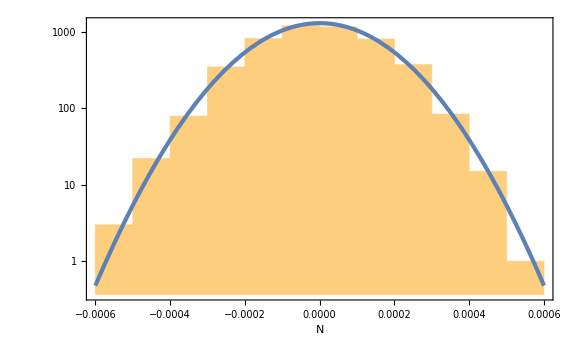

```mathematica
Show[Histogram[NclMap-NclMean,ScalingFunctions->"Log",FrameLabel->{"N",None}],LogPlot[(num^3 0.0001)/Sqrt[2π σ2] Exp[-x^2/(2σ2)]/.{σ2->Variance[NclMap]},{x,-0.0006,0.0006}]]
```

```mathematica
zeta=Table[NclMap[[num^2 (nz-1)+num(ny-1)+nx]]-NclMean,{nz,num},{ny,num},{nx,num}];
```

```mathematica
Dzeta=3Sqrt[Variance[zeta//Flatten]]
```

0.000433454

```mathematica
ListDensityPlot3D[zeta,BoxRatios->{1, 1, 1},Ticks->None,ColorFunction->(ColorData["TemperatureMap"][(#1/Dzeta+1)/2]&),ColorFunctionScaling->False,PlotLegends->BarLegend[{Automatic,{-Dzeta,Dzeta}},LegendLabel->OverTilde[ζ]==-H δρ/ρ̇,LabelStyle->Directive[Large,Black,FontFamily->"Palatino"]],ImageSize->Large]
```

-Graphics3D-

```mathematica
ListDensityPlot3D[zeta,BoxRatios->{1, 1, 1},ColorFunction->(ColorData["TemperatureMap"][(#1/Dzeta+1)/2]&),ColorFunctionScaling->False,Ticks->None,ImageSize->Large,ViewPoint->Left,Boxed->False,Axes->False]
```

-Graphics3D-

```mathematica
(** Fourier transformation 1<kx<num **)
```

```mathematica
ζk[kx_,ky_,kz_]=1/num^(3/2)Sum[zeta[[xz,xy,xx]] ⅇ^(-(2π ⅈ)/num((xx-1)(kx-1)+(xy-1)(ky-1)+(xz-1)(kz-1))),{xx,num},{xy,num},{xz,num}];
```

```mathematica
(** Count Subscript[N, k] **)
```

```mathematica
norm3[x_,y_,z_]=√((x-1)^2+(y-1)^2+(z-1)^2);
```

```mathematica
normdat=Table[Table[Table[norm3[nx,ny,nz],{nx,num}],{ny,num}],{nz,num}]//Simplify;
```

```mathematica
ck=0.01;
```

```mathematica
lnk[ll_]=(1+ck)^(ll-1)-1;
```

```mathematica
klist={};lk=0;
```

```mathematica
Do[If[lnk[ii]<√3(num-1),klist=Join[klist,{lnk[ii]}];lk++;,Break;],{ii,1,1000}]
klist=Join[klist,{lnk[lk+1]}];
ksize=klist//Length;
```

```mathematica
Nklist=Table[Length[Select[Select[Flatten[Flatten[normdat]],#≥lnk[nk]&],#<lnk[nk+1]&]],{nk,ksize}];
```

```mathematica
Nk=0;ζtemp=0;
```

```mathematica
ζeList[ii_]:=Select[Flatten[Table[If[klist[[ii]]<=norm3[nx,ny,nz]<klist[[ii+1]],Abs[ζk[nx,ny,nz]]^2,None],{nz,num},{ny,num},{nx,num}],2],Positive]
```

```mathematica
ζe=Table[ζeList[ii],{ii,ksize-1}];//AbsoluteTiming
ζt=Table[Total[ζe[[ii]]],{ii,Length[ζe]}];
```

{97.2263,Null}

```mathematica
tab=Table[Around[Sum[ζe[[jj,ll]],{ll,Length[ζe[[jj]]]}],If[Length[ζe[[jj]]]>1,Sqrt[Nklist[[jj]]]StandardDeviation[ζe[[jj]]],0]],{jj,Length[ζe]}];
```

```mathematica
taberr=Table[{klist[[ii]],tab[[ii]]/(num^3 ck)},{ii,Length[tab]}];
```

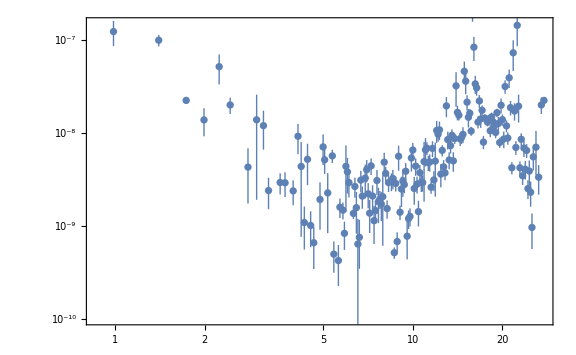

```mathematica
ListLogLogPlot[taberr,PlotRange->{10^-10,1.5 10^-7},Frame->True,Joined->False]
```

```mathematica
(** Check the variance **)
```

```mathematica
flatζ=zeta//Flatten;
```

```mathematica
(*num^-3(flatdN.flatdN)*)
Variance[flatζ]
```

2.08758×10^-8

```mathematica
ck Total[ζt]/(num^3 ck)
```

2.08716×10^-8

## Lattice (inflection)

### Annimation

```mathematica
LatticeMapData=Import["Lattice_inflection.dat"];
```

```mathematica
num=Length[First[LatticeMapData]]^(1/3)
```

17

```mathematica
zetaList=Table[LatticeMapData[[efoldN,num^2 (nz-1)+num(ny-1)+nx]],{efoldN,Length[LatticeMapData]},{nx,num},{ny,num},{nz,num}];
```

```mathematica
Dzeta=3Sqrt[Variance[Last[zetaList]//Flatten]]
```

0.169061

```mathematica
zetaPlotList=Table[ListDensityPlot3D[zetaList[[i]],BoxRatios->{1, 1, 1},Ticks->None,ColorFunction->(ColorData["TemperatureMap"][(#1/Dzeta+1)/2]&),ColorFunctionScaling->False,PlotLegends->BarLegend[{Automatic,{-Dzeta,Dzeta}},LegendLabel->OverTilde[ζ]==-H δρ/ρ̇,LabelStyle->Directive[Large,Black,FontFamily->"Palatino"]],PlotLabel->Style[N==0.1(i-1),Large,Black,FontFamily->"Palatino"],ImageSize->Large],{i,2,Length[zetaList]}];
```

```mathematica
Export["zetamap_inflection.gif",zetaPlotList];//AbsoluteTiming
```

{38.0546,Null}

```mathematica
Last[zetaPlotList]
```

-Graphics3D-

### Power Spectrum

```mathematica
NclMap=Map[#[[2]]&,Sort[Import["Ncl_inflection.dat"]]];
```

```mathematica
num=Length[NclMap]^(1/3)
```

17

```mathematica
NclMean=Mean[NclMap]
```

19.6399

```mathematica
Variance[NclMap]
```

0.00312366

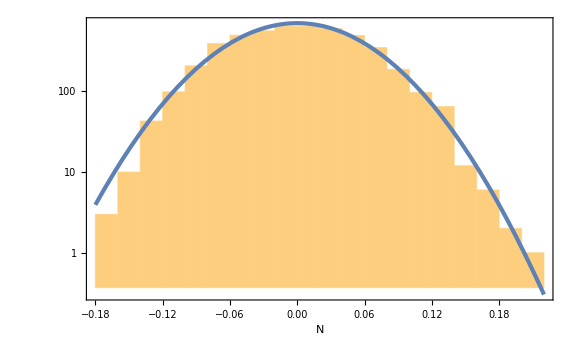

```mathematica
Show[Histogram[NclMap-NclMean,ScalingFunctions->"Log",FrameLabel->{"N",None}],LogPlot[(num^3 0.02)/Sqrt[2π σ2] Exp[-x^2/(2σ2)]/.{σ2->Variance[NclMap]},{x,-0.18,0.22}]]
```

```mathematica
zeta=Table[NclMap[[num^2 (nz-1)+num(ny-1)+nx]]-NclMean,{nz,num},{ny,num},{nx,num}];
```

```mathematica
Dzeta=3Sqrt[Variance[zeta//Flatten]]
```

0.167669

```mathematica
ListDensityPlot3D[zeta,BoxRatios->{1, 1, 1},Ticks->None,ColorFunction->(ColorData["TemperatureMap"][(#1/Dzeta+1)/2]&),ColorFunctionScaling->False,PlotLegends->BarLegend[{Automatic,{-Dzeta,Dzeta}},LegendLabel->OverTilde[ζ]==-H δρ/ρ̇,LabelStyle->Directive[Large,Black,FontFamily->"Palatino"]],ImageSize->Large]
```

-Graphics3D-

```mathematica
ListDensityPlot3D[zeta,BoxRatios->{1, 1, 1},ColorFunction->(ColorData["TemperatureMap"][(#1/Dzeta+1)/2]&),ColorFunctionScaling->False,Ticks->None,ImageSize->Large,ViewPoint->Back,Boxed->False,Axes->False]
```

-Graphics3D-

```mathematica
(** Fourier transformation 1<kx<num **)
```

```mathematica
ζk[kx_,ky_,kz_]=1/num^(3/2)Sum[zeta[[xz,xy,xx]] ⅇ^(-(2π ⅈ)/num((xx-1)(kx-1)+(xy-1)(ky-1)+(xz-1)(kz-1))),{xx,num},{xy,num},{xz,num}];
```

```mathematica
(** Count Subscript[N, k] **)
```

```mathematica
norm3[x_,y_,z_]=√((x-1)^2+(y-1)^2+(z-1)^2);
```

```mathematica
normdat=Table[Table[Table[norm3[nx,ny,nz],{nx,num}],{ny,num}],{nz,num}]//Simplify;
```

```mathematica
ck=0.01;
```

```mathematica
lnk[ll_]=(1+ck)^(ll-1)-1;
```

```mathematica
klist={};lk=0;
```

```mathematica
Do[If[lnk[ii]<√3(num-1),klist=Join[klist,{lnk[ii]}];lk++;,Break;],{ii,1,1000}]
klist=Join[klist,{lnk[lk+1]}];
ksize=klist//Length;
```

```mathematica
Nklist=Table[Length[Select[Select[Flatten[Flatten[normdat]],#≥lnk[nk]&],#<lnk[nk+1]&]],{nk,ksize}];
```

```mathematica
Nk=0;ζtemp=0;
```

```mathematica
ζeList[ii_]:=Select[Flatten[Table[If[klist[[ii]]<=norm3[nx,ny,nz]<klist[[ii+1]],Abs[ζk[nx,ny,nz]]^2,None],{nz,num},{ny,num},{nx,num}],2],Positive]
```

```mathematica
ζe=ParallelTable[ζeList[ii],{ii,ksize-1}];//AbsoluteTiming
ζt=Table[Total[ζe[[ii]]],{ii,Length[ζe]}];
```

{28.7234,Null}

```mathematica
tab=Table[Around[Sum[ζe[[jj,ll]],{ll,Length[ζe[[jj]]]}],If[Length[ζe[[jj]]]>1,Sqrt[Nklist[[jj]]]StandardDeviation[ζe[[jj]]],0]],{jj,Length[ζe]}];
```

```mathematica
taberr=Table[{klist[[ii]],tab[[ii]]/(num^3 ck)},{ii,Length[tab]}];
```

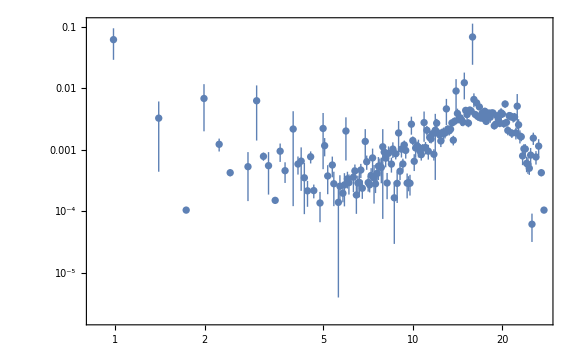

```mathematica
ListLogLogPlot[taberr,(*PlotRange->{10^-10,1.5 10^-7},*)Frame->True,Joined->False]
```

```mathematica
(** Check the variance **)
```

```mathematica
flatζ=zeta//Flatten;
```

```mathematica
(*num^-3(flatdN.flatdN)*)
Variance[flatζ]
```

0.00433627

```mathematica
ck Total[ζt]/(num^3 ck)
```

0.00433538

## Lattice (chaotic_biased)

```mathematica
V[x_]=1/2 m^2 x^2;
ϵV[x_]=1/2(V'[x]/V[x])^2;
```

```mathematica
1/(24 π^2)V[x]/ϵV[x]/.{x->15,m->10^-5}//N
```

5.34311×10^-9

```mathematica
Solve[1/(24 π^2)V[x]/ϵV[x]==10^-2,m][[2]]/.{x->15}//N
```

{m→0.0136805}

### Annimation

```mathematica
LatticeMapData=Import["Lattice_chaotic_biased.dat"];
```

```mathematica
num=Length[First[LatticeMapData]]^(1/3)
```

17

```mathematica
ksigma[NN_]=(2π σ E^NN)/num/.{σ->10^-1};
```

```mathematica
(2π)/ksigma[3]//N
```

8.4638

```mathematica
zetaList=Table[LatticeMapData[[efoldN,num^2 (nz-1)+num(ny-1)+nx]],{efoldN,Length[LatticeMapData]},{nx,num},{ny,num},{nz,num}];
```

```mathematica
Dzeta=3Sqrt[Variance[Last[zetaList]//Flatten]]
```

1.39454

```mathematica
zetaPlotList=Table[ListDensityPlot3D[zetaList[[i]],BoxRatios->{1, 1, 1},Ticks->None,ColorFunction->(ColorData["TemperatureMap"][(#1/Dzeta+1)/2]&),ColorFunctionScaling->False,PlotLegends->BarLegend[{Automatic,{-Dzeta,Dzeta}},LegendLabel->OverTilde[ζ]==-H δρ/ρ̇,LabelStyle->Directive[Large,Black,FontFamily->"Palatino"]],PlotLabel->Style[N==0.1(i-1),Large,Black,FontFamily->"Palatino"],ImageSize->Large],{i,2,Length[zetaList]}];
```

```mathematica
Export["zetamap_chaotic_biased.gif",zetaPlotList];//AbsoluteTiming
```

{38.4011,Null}

```mathematica
Last[zetaPlotList]
```

-Graphics3D-

### Power Spectrum

```mathematica
NclMap=Map[#[[2]]&,Sort[Import["Ncl_chaotic_biased.dat"]]];
```

```mathematica
num=Length[NclMap]^(1/3)
```

17

```mathematica
NclMean=Mean[NclMap]
```

57.0458

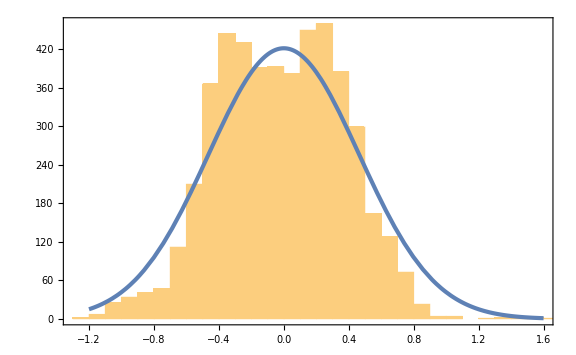

```mathematica
Show[Histogram[NclMap-NclMean],Plot[(num^3 0.1)/Sqrt[2π σ2] Exp[-x^2/(2σ2)]/.{σ2->Variance[NclMap]},{x,-1.2,1.6}]]
```

```mathematica
zeta=Table[NclMap[[num^2 (nz-1)+num(ny-1)+nx]]-NclMean,{nz,num},{ny,num},{nx,num}];
```

```mathematica
Dzeta=3Sqrt[Variance[zeta//Flatten]]
```

1.39451

```mathematica
dNFig=ListDensityPlot3D[zeta,BoxRatios->{1, 1, 1},Ticks->None,ColorFunction->(ColorData["TemperatureMap"][(#1/Dzeta+1)/2]&),ColorFunctionScaling->False,PlotLegends->BarLegend[{Automatic,{-Dzeta,Dzeta}},LegendLabel->OverTilde[ζ]==-H δρ/ρ̇,LabelStyle->Directive[Large,Black,FontFamily->"Palatino"]],ImageSize->Large]
```

-Graphics3D-

```mathematica
Export["zetamap_chaotic_biased.pdf",dNFig];
```

```mathematica
dr=1;
Clear[zetardata]
zetardata[r_]:=Select[Flatten[Table[If[(r-dr/2)^2<=(i-1)^2+(j-1)^2+(k-1)^2<(r+dr/2)^2,zeta[[i,j,k]],None],{i,num},{j,num},{k,num}],2],NumberQ]
```

```mathematica
zetarList=Select[Table[zetardatas=zetardata[r];If[Length[zetardatas]>1,{r,Mean[zetardatas]±StandardDeviation[zetardatas]/Sqrt[Length[zetardatas]]},None],{r,1,num Sqrt[3]}],Length[#]>1&];
zetarListwoError=Select[Table[zetardatas=zetardata[r];If[Length[zetardatas]>1,{r,Mean[zetardatas]},None],{r,1,num Sqrt[3]}],Length[#]>1&];
```

```mathematica
ksigma[NN_]=(2π σ E^NN)/num/.{σ->10^-1};
```

```mathematica
fit=FindFit[zetarListwoError,A Sin[ksigma[3]r]/(ksigma[3]r),A,r]
```

{A→4.8519}

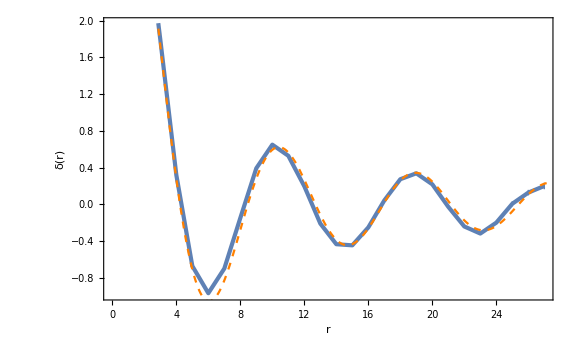

```mathematica
Show[ListPlot[zetarList,FrameLabel->{r,"δ(r)"},PlotLegends->Placed[LineLegend[{"lattice"},LegendMarkerSize->30],{0.8,0.8}]],Plot[A Sin[ksigma[3]r]/(ksigma[3]r)/.fit,{r,0,num Sqrt[3]},PlotStyle->{Orange,Dashed},PlotLegends->Placed[LineLegend[{"(sin (SubscriptBox[k, σ] r))/k_σ"},LegendMarkerSize->30],{0.8,0.8}]]]
```

```mathematica
ListDensityPlot3D[zeta,BoxRatios->{1, 1, 1},ColorFunction->(ColorData["TemperatureMap"][(#1/Dzeta+1)/2]&),ColorFunctionScaling->False,Ticks->None,ImageSize->Large,ViewPoint->Left,Boxed->False,Axes->False]
```

-Graphics3D-

```mathematica
(** Fourier transformation 1<kx<num **)
```

```mathematica
ζk[kx_,ky_,kz_]=1/num^(3/2)Sum[zeta[[xz,xy,xx]] ⅇ^(-(2π ⅈ)/num((xx-1)(kx-1)+(xy-1)(ky-1)+(xz-1)(kz-1))),{xx,num},{xy,num},{xz,num}];
```

```mathematica
(** Count Subscript[N, k] **)
```

```mathematica
norm3[x_,y_,z_]=√((x-1)^2+(y-1)^2+(z-1)^2);
```

```mathematica
normdat=Table[Table[Table[norm3[nx,ny,nz],{nx,num}],{ny,num}],{nz,num}]//Simplify;
```

```mathematica
ck=0.01;
```

```mathematica
lnk[ll_]=(1+ck)^(ll-1)-1;
```

```mathematica
klist={};lk=0;
```

```mathematica
Do[If[lnk[ii]<√3(num-1),klist=Join[klist,{lnk[ii]}];lk++;,Break;],{ii,1,1000}]
klist=Join[klist,{lnk[lk+1]}];
ksize=klist//Length;
```

```mathematica
Nklist=Table[Length[Select[Select[Flatten[Flatten[normdat]],#≥lnk[nk]&],#<lnk[nk+1]&]],{nk,ksize}];
```

```mathematica
Nk=0;ζtemp=0;
```

```mathematica
ζeList[ii_]:=Select[Flatten[Table[If[klist[[ii]]<=norm3[nx,ny,nz]<klist[[ii+1]],Abs[ζk[nx,ny,nz]]^2,None],{nz,num},{ny,num},{nx,num}],2],Positive]
```

```mathematica
ζe=Table[ζeList[ii],{ii,ksize-1}];//AbsoluteTiming
ζt=Table[Total[ζe[[ii]]],{ii,Length[ζe]}];
```

{2.23542,Null}

```mathematica
tab=Table[Around[Sum[ζe[[jj,ll]],{ll,Length[ζe[[jj]]]}],If[Length[ζe[[jj]]]>1,Sqrt[Nklist[[jj]]]StandardDeviation[ζe[[jj]]],0]],{jj,Length[ζe]}];
```

```mathematica
taberr=Table[{klist[[ii]],tab[[ii]]/(num^3 ck)},{ii,Length[tab]}];
```

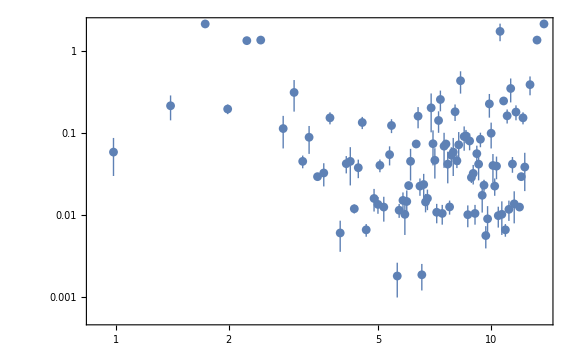

```mathematica
ListLogLogPlot[taberr(*,PlotRange->{10^-10,1.5 10^-7}*),Frame->True,Joined->False]
```

```mathematica
(** Check the variance **)
```

```mathematica
flatζ=zeta//Flatten;
```

```mathematica
(*num^-3(flatdN.flatdN)*)
Variance[flatζ]
```

0.169722

```mathematica
ck Total[ζt]/(num^3 ck)
```

0.169489

## Lattice (inflection_biased)

### Annimation

```mathematica
LatticeMapData=Import["Lattice_inflection_biased.dat"];
```

```mathematica
num=Length[First[LatticeMapData]]^(1/3)
```

17

```mathematica
zetaList=Table[LatticeMapData[[efoldN,num^2 (nz-1)+num(ny-1)+nx]],{efoldN,Length[LatticeMapData]},{nx,num},{ny,num},{nz,num}];
```

```mathematica
Dzeta=3Sqrt[Variance[Last[zetaList]//Flatten]]
```

1.17396

```mathematica
zetaPlotList=Table[ListDensityPlot3D[zetaList[[i]],BoxRatios->{1, 1, 1},Ticks->None,ColorFunction->(ColorData["TemperatureMap"][(#1/Dzeta+1)/2]&),ColorFunctionScaling->False,PlotLegends->BarLegend[{Automatic,{-Dzeta,Dzeta}},LegendLabel->OverTilde[ζ]==-H δρ/ρ̇,LabelStyle->Directive[Large,Black,FontFamily->"Palatino"]],PlotLabel->Style[N==0.1(i-1),Large,Black,FontFamily->"Palatino"],ImageSize->Large],{i,2,Length[zetaList]}];
```

```mathematica
Export["zetamap_inflection_biased.gif",zetaPlotList];//AbsoluteTiming
```

{38.9137,Null}

```mathematica
Last[zetaPlotList]
```

-Graphics3D-

### Power Spectrum

```mathematica
NclMap=Map[#[[2]]&,Sort[Import["Ncl_inflection_biased.dat"]]];
```

```mathematica
num=Length[NclMap]^(1/3)
```

17

```mathematica
NclMean=Mean[NclMap]
```

19.6769

```mathematica
zeta=Table[NclMap[[num^2 (nz-1)+num(ny-1)+nx]]-NclMean,{nz,num},{ny,num},{nx,num}];
```

```mathematica
Dzeta=3Sqrt[Variance[zeta//Flatten]]
```

0.485772

```mathematica
dNFig=ListDensityPlot3D[zeta,BoxRatios->{1, 1, 1},Ticks->None,ColorFunction->(ColorData["TemperatureMap"][(#1/Dzeta+1)/2]&),ColorFunctionScaling->False,PlotLegends->BarLegend[{Automatic,{-Dzeta,Dzeta}},LegendLabel->OverTilde[ζ]==-H δρ/ρ̇,LabelStyle->Directive[Large,Black,FontFamily->"Palatino"]],ImageSize->Large]
```

-Graphics3D-

```mathematica
Export["zetamap_inflection_biased.pdf",dNFig];
```

```mathematica
dr=1;
Clear[zetardata]
zetardata[r_]:=Select[Flatten[Table[If[(r-dr/2)^2<=(i-1)^2+(j-1)^2+(k-1)^2<(r+dr/2)^2,zeta[[i,j,k]],None],{i,num},{j,num},{k,num}],2],NumberQ]
```

```mathematica
zetarList=Select[ParallelTable[zetardatas=zetardata[r];If[Length[zetardatas]>1,{r,Mean[zetardatas]±StandardDeviation[zetardatas]/Sqrt[Length[zetardatas]]},None],{r,1,num Sqrt[3]}],Length[#]>1&];
zetarListwoError=Select[ParallelTable[zetardatas=zetardata[r];If[Length[zetardatas]>1,{r,Mean[zetardatas]},None],{r,1,num Sqrt[3]}],Length[#]>1&];
```

```mathematica
ksigma[NN_]=(2π σ E^NN)/num/.{σ->10^-1};
```

```mathematica
fit=FindFit[zetarListwoError,A Sin[ksigma[3]r]/(ksigma[3]r),A,r]
```

{A→1.96404}

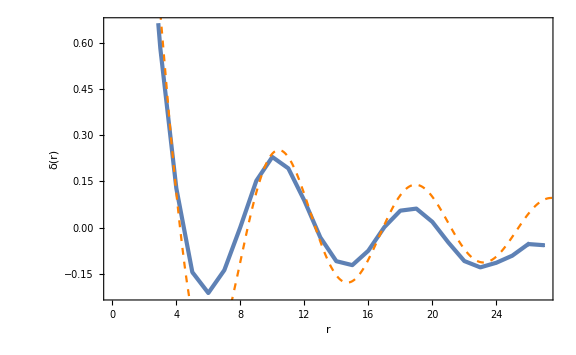

```mathematica
Show[ListPlot[zetarList,FrameLabel->{r,"δ(r)"},PlotLegends->Placed[LineLegend[{"lattice"},LegendMarkerSize->30],{0.8,0.8}]],Plot[A Sin[ksigma[3]r]/(ksigma[3]r)/.fit,{r,0,num Sqrt[3]},PlotStyle->{Orange,Dashed},PlotLegends->Placed[LineLegend[{"(sin (SubscriptBox[k, σ] r))/k_σ"},LegendMarkerSize->30],{0.8,0.8}]]]
```

```mathematica
ListDensityPlot3D[zeta,BoxRatios->{1, 1, 1},ColorFunction->(ColorData["TemperatureMap"][(#1/Dzeta+1)/2]&),ColorFunctionScaling->False,Ticks->None,ImageSize->Large,ViewPoint->Back,Boxed->False,Axes->False]
```

-Graphics3D-

```mathematica
(** Fourier transformation 1<kx<num **)
```

```mathematica
ζk[kx_,ky_,kz_]=1/num^(3/2)Sum[zeta[[xz,xy,xx]] ⅇ^(-(2π ⅈ)/num((xx-1)(kx-1)+(xy-1)(ky-1)+(xz-1)(kz-1))),{xx,num},{xy,num},{xz,num}];
```

```mathematica
(** Count Subscript[N, k] **)
```

```mathematica
norm3[x_,y_,z_]=√((x-1)^2+(y-1)^2+(z-1)^2);
```

```mathematica
normdat=Table[Table[Table[norm3[nx,ny,nz],{nx,num}],{ny,num}],{nz,num}]//Simplify;
```

```mathematica
ck=0.01;
```

```mathematica
lnk[ll_]=(1+ck)^(ll-1)-1;
```

```mathematica
klist={};lk=0;
```

```mathematica
Do[If[lnk[ii]<√3(num-1),klist=Join[klist,{lnk[ii]}];lk++;,Break;],{ii,1,1000}]
klist=Join[klist,{lnk[lk+1]}];
ksize=klist//Length;
```

```mathematica
Nklist=Table[Length[Select[Select[Flatten[Flatten[normdat]],#≥lnk[nk]&],#<lnk[nk+1]&]],{nk,ksize}];
```

```mathematica
Nk=0;ζtemp=0;
```

```mathematica
ζeList[ii_]:=Select[Flatten[Table[If[klist[[ii]]<=norm3[nx,ny,nz]<klist[[ii+1]],Abs[ζk[nx,ny,nz]]^2,None],{nz,num},{ny,num},{nx,num}],2],Positive]
```

```mathematica
ζe=ParallelTable[ζeList[ii],{ii,ksize-1}];//AbsoluteTiming
ζt=Table[Total[ζe[[ii]]],{ii,Length[ζe]}];
```

{0.945434,Null}

```mathematica
tab=Table[Around[Sum[ζe[[jj,ll]],{ll,Length[ζe[[jj]]]}],If[Length[ζe[[jj]]]>1,Sqrt[Nklist[[jj]]]StandardDeviation[ζe[[jj]]],0]],{jj,Length[ζe]}];
```

```mathematica
taberr=Table[{klist[[ii]],tab[[ii]]/(num^3 ck)},{ii,Length[tab]}];
```

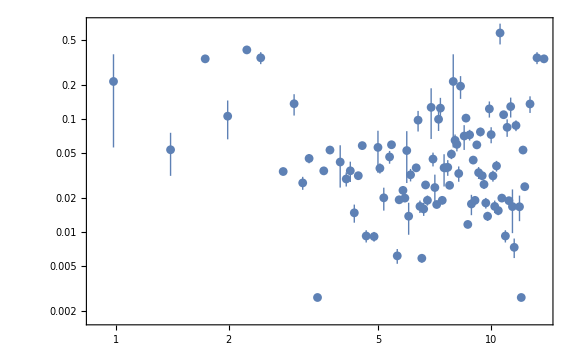

```mathematica
ListLogLogPlot[taberr,(*PlotRange->{10^-10,1.5 10^-7},*)Frame->True,Joined->False]
```

```mathematica
(** Check the variance **)
```

```mathematica
flatζ=zeta//Flatten;
```

```mathematica
(*num^-3(flatdN.flatdN)*)
Variance[flatζ]
```

0.0669521

```mathematica
ck Total[ζt]/(num^3 ck)
```

0.0668603